# Calculating mathematial constants using Monte Carlo simulations

Bhoris Dhanjal

## Section 1: Naive Monte Carlo Integration

```mathematica
g[x_]=100-8x^2+x^3;
```

```mathematica
a=2;b=5;
```

```mathematica
IntegralPlot[f_,{x_,L_,U_},{l_,u_},opts:OptionsPattern[]]:=Module[{col=ColorData[1,1]},Plot[{ConditionalExpression[f,x>l&&x<u],f},{x,L,U},Prolog->{{col,Line[{{l,0},{l,f/.{x->l}}}]},{col,Line[{{u,0},{u,f/.{x->u}}}]}},Filling->{1->Axis},PlotStyle->col,opts]]
```

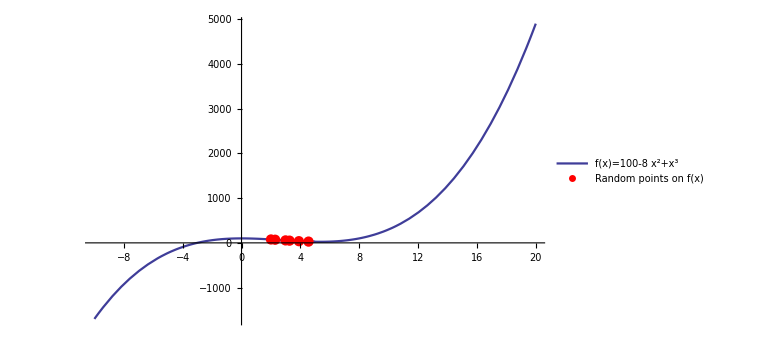

```mathematica
ExampleRand=RandomReal[{a,b},{6}];
ExamplePoints=g[ExampleRand];
pexample=Show[IntegralPlot[g[x],{x,-10,20},{2,5},PlotLegends->{TraditionalForm[HoldForm[f[x]=100-8x^2+x^3]]}],ListPlot[Transpose[{ExampleRand,ExamplePoints}],PlotStyle->{Red},PlotLegends->{TraditionalForm[HoldForm[Random points on f[x]]]}],PlotTheme->"Detailed",PlotRange->{{-2,8},{150,0}},AxesOrigin->{0,0},ImageSize->Large]
pexamplenolegend=Show[IntegralPlot[g[x],{x,-10,20},{2,5}],ListPlot[Transpose[{ExampleRand,ExamplePoints}],PlotStyle->{Red}],PlotTheme->"Detailed",PlotRange->{{-2,8},{150,0}},AxesOrigin->{0,0},ImageSize->Large];
```

```mathematica
points=Table[Rectangle[{a,0 },{b,ExamplePoints[[x]]}],{x,1,5}]
```

{Rectangle[{2,0},{5,37.6609}],Rectangle[{2,0},{5,49.5594}],Rectangle[{2,0},{5,28.5325}],Rectangle[{2,0},{5,75.9617}],Rectangle[{2,0},{5,55.1924}]}

```mathematica
rectangles[x_]:={Red,Opacity[0.05],EdgeForm[Red],points};
```

```mathematica
g[x_]:=Show[pexamplenolegend,Graphics[{Red,Opacity[0.3],Rectangle[{2,0},{5,ExamplePoints[[x]]}],ImageSize->Medium}]];
```

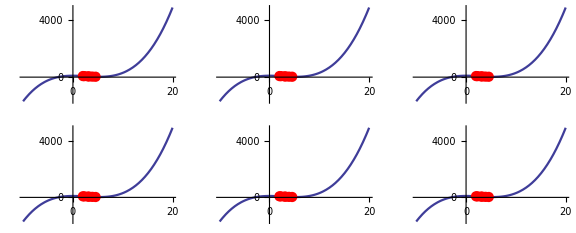

```mathematica
GraphicsGrid[{{g[4],g[6],g[5]},{g[2],g[1],g[3]}},ImageSize->Large]
```

## Section 2: Estimating Pi

### 2.1 Elementary Method

```mathematica
pairs=RandomReal[{-1,1},{10000,2}];
4 Count[Map[Norm,pairs],_?(#≤1&)]/10000.
```

3.1512

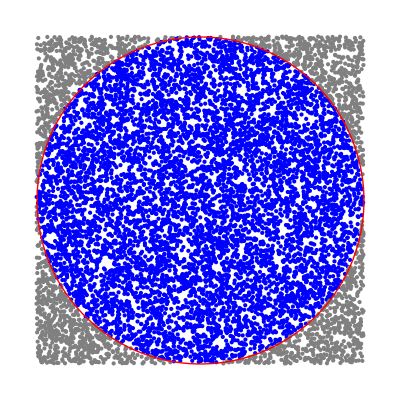

```mathematica
Graphics[{PointSize[Small],Blue,Point@Select[pairs,Norm[#]≤1&],Gray,Point@Select[pairs,Norm[#]>1&],Red,Thick,Circle[]},AspectRatio->1]
```

```mathematica
approxPi[n_]:=4. Count[Map[Norm,RandomReal[{-1,1},{n,2}]],_?(#≤1&)]/n
```

```mathematica
RepeatedExperiment=ParallelTable[approxPi[10^6],{10^3}];//AbsoluteTiming
```

{263.747,Null}

```mathematica
mupi=Mean[RepeatedExperiment]
```

3.14154

```mathematica
NumberForm[mupi,10]
```

3.141539388

```mathematica
(3.141539388-Pi)/Pi*100
```

-0.0016955

```mathematica
sigmapi=StandardDeviation[RepeatedExperiment]
```

0.00165069

```mathematica
NumberForm[sigmapi,10]
```

0.001650685944

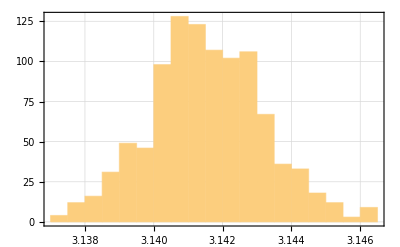

```mathematica
Histogram[RepeatedExperiment,PlotTheme->"Detailed"]
```

### 2.2 Buffon' s Needle

```mathematica
BuffonsNeedle[r_,{x_,y_},n_]:=Module[
{
data=Table[{{x Random[Real],y Random[Real]},π Random[Real]},{n}],
lines,hits,misses
},
Graphics[lines=(Function[s,First[#]+s  r/2 Through[{Cos,Sin}[Last[#]]]]/@{1,-1})&/@data;
{
Line[{{#,0},{#,y}}]&/@Range[0,Ceiling[x]],
PointSize[.01],
{misses,hits}=Map[Last,Split[Sort[Transpose[{Abs[Subtract@@(Floor/@First/@#)&/@lines],lines}]],(First[#1]==First[#2]&)],{2}];
Transpose[{
{RGBColor[1,.47,0],RGBColor[.67,.75,.15]},
{Line/@#}&/@{hits,misses}
}]
}, PlotLabel-> Column[{
Style[
Row[{"hit ratio: ",ToString[TraditionalForm["hits"/"N"]]," = ",With[{a=Length[hits],b=n},HoldForm[a/b]]," ~~ ",ToString[Round[100Length[hits]/n]],"%"}],"Label"],
Style[
Row[{"π"," ~~ ",ToString[TraditionalForm[("2 x L x N")/"hits"]]," = ",With[{a=Length[hits],b=n, c=r},HoldForm[(2c b)/a]]," ~~ ",ToString[N[2n r/Length[hits]]]}],
"Label"]}],PlotRange->{{-1/2,x+1/2},{-1/2,y+1/2}},ImageSize->{400,300}]
];
```

```mathematica
Manipulate[SeedRandom[sr];BuffonsNeedle[length,{10,6},needles],{{needles,200,"number of needles (N)"},20,1000,1,Appearance-> "Labeled"},{{length,.6,"needle length (L)"},.25,1,Appearance-> "Labeled"},{{sr,12,"random seed"},1,100,1},SaveDefinitions->True]
```

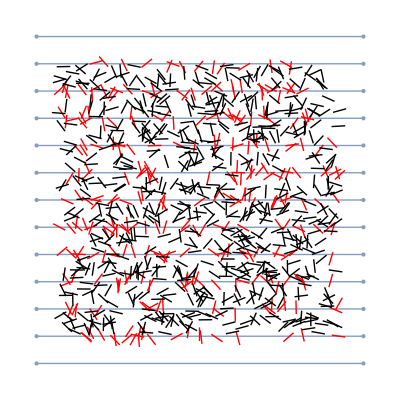

3.14465

```mathematica
d=0.2;n=1000;
lines=MeshRegion[Join@@Table[{{-1-d,y},{1+d,y}},{y,-1-d,1+d,d}],Line[Partition[Range[2 Floor[2/d+3]],2]]];
needles=Table[Line[{pt,RandomPoint[Circle[pt,0.5d]]}],{pt,RandomReal[{-1,1},{n,2}]}];
overlap=Select[needles,!RegionDisjoint[lines,#]&];
Show[lines,Graphics[{Red,overlap,Black,Complement[needles,overlap]}]]
N[( n)/Length[overlap]]
```

```mathematica
NewRepeatedBuffon=ParallelTable[d=0.2;n=10000;
lines=MeshRegion[Join@@Table[{{-1-d,y},{1+d,y}},{y,-1-d,1+d,d}],Line[Partition[Range[2 Floor[2/d+3]],2]]];
needles=Table[Line[{pt,RandomPoint[Circle[pt,0.5d]]}],{pt,RandomReal[{-1,1},{n,2}]}];
overlap=Select[needles,!RegionDisjoint[lines,#]&];
N[( n)/Length[overlap]], {10^3}];//AbsoluteTiming
```

{2607.03,Null}

```mathematica
Mean[NewRepeatedBuffon]
```

3.14018

```mathematica
StandardDeviation[NewRepeatedBuffon]
```

0.0451035

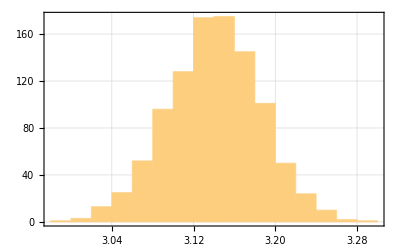

```mathematica
Histogram[NewRepeatedBuffon,PlotTheme->"Detailed"]
```

```mathematica
ScientificForm[100(Mean[NewRepeatedBuffon]-Pi)/Pi]
```

-4.4808×10^-2

### 2.3 Buffon' s Noodle

```mathematica
generateNoodle[l_,np_,cent_]:=Block[{ls=l/np,pts},pts=RandomPoint[Circle[{0,0},ls],np];
Line/@Partition[(cent+#)&/@Accumulate[pts],2,1]]
```

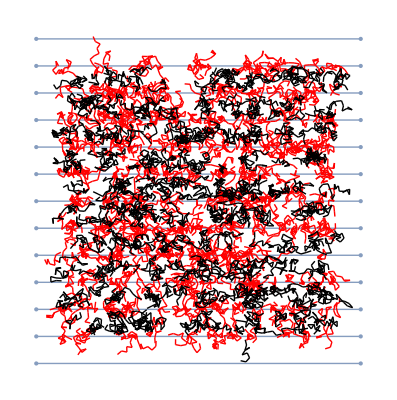

3.36984

```mathematica
d=0.2;n=1000;
lines=MeshRegion[Join@@Table[{{-1-d,y},{1+d,y}},{y,-1-d,1+d,d}],Line[Partition[Range[2 Floor[2/d+3]],2]]];
noodles=Table[generateNoodle[d,10,pt],{pt,RandomReal[{-1,1},{n,2}]}];
ints=With[{nood=#},RegionDisjoint[#,lines]&/@nood]&/@noodles;
overlap=Extract[noodles,Position[And@@#&/@ints,False]];
Show[lines,Graphics[{Red,overlap,Black,Complement[noodles,overlap]}]]
N[(2n l)/(Count[ints,False,2]d)]
```

```mathematica
ParallelRepeatedBuffonNoodle=ParallelTable[d=0.2;n=10000;
lines=MeshRegion[Join@@Table[{{-1-d,y},{1+d,y}},{y,-1-d,1+d,d}],Line[Partition[Range[2 Floor[2/d+3]],2]]];
noodles=Table[generateNoodle[d,RandomInteger[{2,10}],pt],{pt,RandomReal[{-1,1},{n,2}]}];
ints=With[{nood=#},RegionDisjoint[#,lines]&/@nood]&/@noodles;
overlap=Extract[noodles,Position[And@@#&/@ints,False]];
n/Length[overlap],250];//AbsoluteTiming
```

{2228.07,Null}

```mathematica
noodlemean=Mean[ParallelRepeatedBuffonNoodle];
N[noodlemean,15]
noodlesigma=StandardDeviation[ParallelRepeatedBuffonNoodle];
N[noodlesigma,15]
```

3.18614572347265

0.0460212421729219

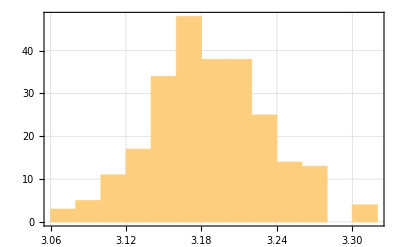

```mathematica
Histogram[ParallelRepeatedBuffonNoodle,PlotTheme->"Detailed"]
```

```mathematica
ScientificForm[100 (3.18614572347265209967236329853743264869-Pi)/Pi]
```

1.418168260355127609859548401751501529

## Section 3: Euler-Mascheroni Constant and Stieltjes Constants

### 3.1 Estimating Euler-Mascheroni Constant by Gumbel Distribution

```mathematica
approxgamma[n_]:=Mean[-Log[-Log[RandomReal[{0,1},{n}]]]]
```

```mathematica
approxgamma[10^6]
```

0.577385

```mathematica
RepeatedGammaExp[n_,repeat_]:=ParallelTable[approxgamma[n], {repeat}];
```

```mathematica
gammaresult=RepeatedGammaExp[10^6,10^4];//AbsoluteTiming
```

{313.266,Null}

```mathematica
mugamma=Mean[gammaresult]
```

0.577213

```mathematica
sigmagamma=StandardDeviation[gammaresult]
```

0.00128127

```mathematica
N[100(mugamma-EulerGamma)/EulerGamma]
```

-0.000482422

```mathematica
ScientificForm[-0.00048242230142396276]
```

-4.82422×10^-4

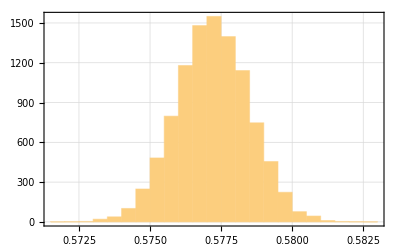

```mathematica
Histogram[gammaresult,PlotTheme->"Detailed"]
```

### 3.2 Estimating Stieltjes constants by approximating an integral

```mathematica
Needs["Compile`"]
```

```mathematica
sub=2000;
tlist=Subdivide[0.,2. Pi,sub];
zeta=Zeta[1.+Exp[I tlist]];
cF=With[{zeta=zeta,tlist=tlist,L=sub/(2. Pi)},Compile[{{t,_Real}},Block[{i,λ},i=Floor[Mod[t,2. Pi] L]+1;
λ=(t-tlist[[i]]) L;
(1.-λ) zeta[[i]]+λ zeta[[i+1]]],CompilationTarget->"C",RuntimeAttributes->{Listable},Parallelization->True,RuntimeOptions->"Speed"]];
sint[n_,x_]:=Exp[-n I x] cF[x]
lowerlim=0.;
upperlim=2. Pi;
ParallelRepeatedStieltjesIntegral[n_,points_,repeat_]:=(((-1)^n n!)/(2. Pi) (upperlim-lowerlim)) ParallelTable[Mean[sint[n,RandomReal[{lowerlim,upperlim},{points}]]],{repeat},Method->"CoarsestGrained"]
```

```mathematica
s1=ParallelRepeatedStieltjesIntegral[1,10^5,10^4];//AbsoluteTiming
```

{52.9252,Null}

```mathematica
Mean[Re[s1]]
```

-0.0728663

```mathematica
StandardDeviation[Re[s1]]
```

0.00258171

```mathematica
ScientificForm[N[100(0.07286628889273356-StieltjesGamma[1])/StieltjesGamma[1]]]
```

-2.00069×10^2

```mathematica
hs1=Histogram[Re[s1],PlotTheme->"Detailed",PlotLabel->Subscript[γ, 1]];
```

```mathematica
s2=ParallelRepeatedStieltjesIntegral[2,10^5,10^4];//AbsoluteTiming
```

{52.1139,Null}

```mathematica
Mean[Re[s2]] 
StandardDeviation[Re[s2]]
```

-0.00969426

0.00523629

```mathematica
ScientificForm[N[100(-0.009694260647498874-StieltjesGamma[2])/StieltjesGamma[2]]]
```

4.02199×10^-2

```mathematica
hs2=Histogram[Re[s2],PlotTheme->"Detailed",PlotLabel->Subscript[γ, 2]];
```

```mathematica
s3=ParallelRepeatedStieltjesIntegral[3,10^5,15000];//AbsoluteTiming
```

{92.3126,Null}

```mathematica
Mean[Re[s3]]
StandardDeviation[Re[s3]]
```

0.00204329

0.0155079

```mathematica
ScientificForm[N[100(0.0020432938187206046-StieltjesGamma[3])/StieltjesGamma[3]]]
```

-5.13216×10^-1

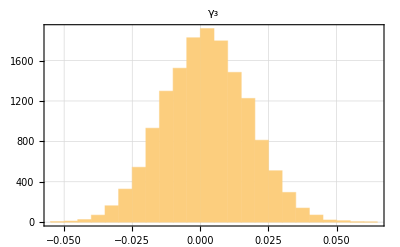

```mathematica
hs3=Histogram[Re[s3],20,PlotTheme->"Detailed",PlotLabel->Subscript[γ, 3]]
```

```mathematica
s4=ParallelRepeatedStieltjesIntegral[4,10^5,30000];//AbsoluteTiming
```

{189.212,Null}

```mathematica
Mean[Re[s4]]
StandardDeviation[Re[s4]]
```

0.00233049

0.0613601

```mathematica
ScientificForm[N[100(0.002330492470272919-StieltjesGamma[4])/StieltjesGamma[4]]]
```

2.20283×10^-1

```mathematica
hs4=Histogram[Re[s4],PlotTheme->"Detailed",PlotLabel->Subscript[γ, 4]];
```

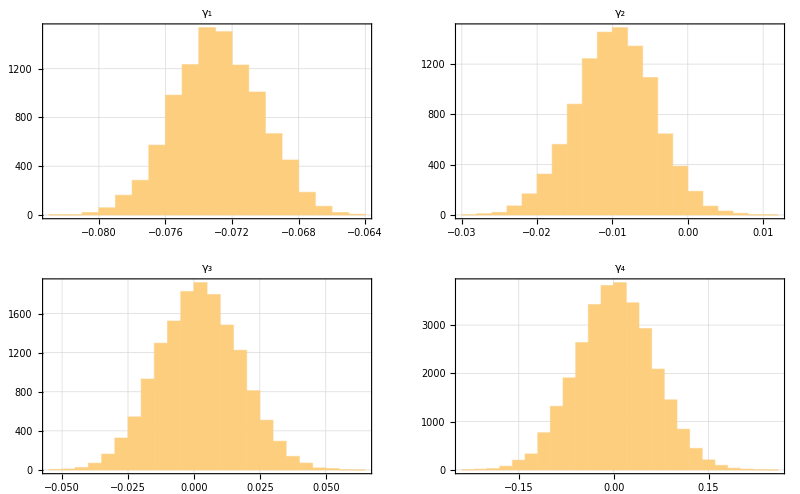

```mathematica
GraphicsGrid[{{hs1,hs2},{hs3,hs4}}]
```

## Section 4: Estimating Euler’s number

```mathematica
ParallelRepeatedEExp[n_,repeat_]:=ParallelTable[Mean[Table[Module[{u=Random[],t=1},While[u<1,u=Random[]+u;t++];t],{n}]],{repeat}]
```

```mathematica
RepeatedEExp=ParallelRepeatedEExp[10^6,10^4];//AbsoluteTiming
```

{1265.84,Null}

```mathematica
muEexp=N[Mean[RepeatedEExp]]
```

2.71827

```mathematica
sigmaEexp=N[StandardDeviation[RepeatedEExp]]
```

0.00087055

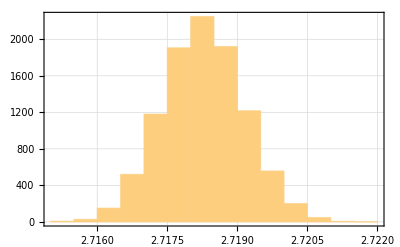

```mathematica
Histogram[RepeatedEExp,PlotTheme->"Detailed"]
```

```mathematica
ScientificForm[N[100 (muEexp-E)/E]]
```

-3.40522×10^-4

## Section 5: Estimating Phi

```mathematica
phiint[x_]=3/2+1/(4Sqrt[x]);
```

```mathematica
phiblim=4;phiulim=5;
```

```mathematica
RepeatedPhiIntegral[points_,repeat_]:=ParallelTable[N[(phiulim-phiblim)/points Total[phiint[RandomReal[{phiblim,phiulim},{points}]]]],{repeat}]
```

```mathematica
PhiIntegralData=RepeatedPhiIntegral[10^6,10^4];//AbsoluteTiming
```

{274.546,Null}

```mathematica
muphi=Mean[PhiIntegralData]
```

1.61803

```mathematica
NumberForm[muphi,10]
```

1.618033999

```mathematica
sigmaphi=StandardDeviation[PhiIntegralData]
```

3.79948×10^-6

```mathematica
N[GoldenRatio,10]
```

1.618033989

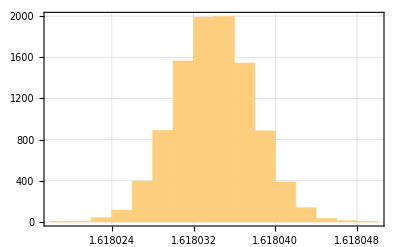

```mathematica
Histogram[PhiIntegralData,PlotTheme->"Detailed"]
```

```mathematica
ScientificForm[N[100 (muphi-GoldenRatio)/GoldenRatio]]
```

6.54299×10^-7